maxR=30

3.64958×10^-9

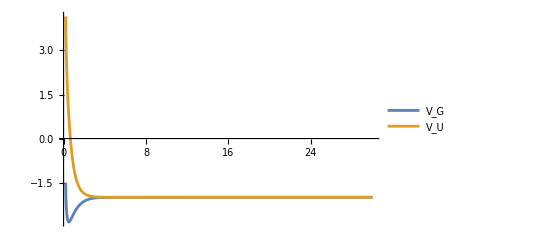

```mathematica
(* Radiative Quenching, Chapter 3 *)
(* This one uses my paper *)

(*electron mass *)
Subscript[m, e]=1;
(* Proton Mass *)
Subscript[m, p]=1836;
(* Reduced Mass *)
μ=Subscript[m, p]/2;
hbar= 1;  
hbarSI =1.054571817*^-34;
cLight=137.036 ;(*SpeedOfLight, atomic units*)
cLightSI= 299792458 ;(*SpeedOfLight, m/s*)
oneSec = 2.418884326509*^-17;  (* 1 sec SI <-> 1 sec AU *)
aBorh = 5.29177*^-11;   (* Si <-> AU *)

(* RawData format R,E, E + 1/R,A,p *)

vSg1RawData = Import["/Users/zelimir/Work/Physics-Thesis/thesis-2/ZelimirOverleaf/MathematicaCodeFinal/gerade1sV2.mx"];
vSu2RawData = Import["/Users/zelimir/Work/Physics-Thesis/thesis-2/ZelimirOverleaf/MathematicaCodeFinal/ungerade1sV2.mx"];

vSg1Data =vSg1RawData[[1;;44]];
vSu2Data = vSu2RawData[[1;;44]];

(* Calculate the Transition Dipole Moment *)
(* Upper Limit for integration *)
maxR = vSg1Data[[Length[vSg1Data]]][[1]];
Print["maxR=",maxR]

(* Load Potential curves for 1sg, 2sg states 
"R","p", "A","E","E+1/r"*)
(* 1sg state, potential curve *)
vG=Interpolation[Transpose[{vSg1Data[[All,1]],vSg1Data[[All,3]]}], InterpolationOrder->3];
(* 2sg state, potential curve *)
vU=Interpolation[Transpose[{vSu2Data[[All,1]],vSu2Data[[All,3]]}], InterpolationOrder->3];

deltaV[r_]:=Abs[vG[r]-vU[r]];
deltaV[20]
Plot[{vG[r],vU[r]},{r,0.2,maxR}, PlotRange->Full, PlotLegends->{"V_G","V_U"}]
```

```mathematica
Print[vSg1Data[[19]][[1]],", ",vSg1Data[[19]][[4]],", ",vSg1Data[[19]][[5]],", ",vSu2Data[[19]][[4]],", ",vSu2Data[[19]][[5]]]
Print[vSg1Data[[20]][[1]],", ",vSg1Data[[20]][[4]],", ",vSg1Data[[20]][[5]],", ",vSu2Data[[20]][[4]],", ",vSu2Data[[20]][[5]]]
```

5., 3437.09, 5.24591, 17397.4, 5.2446

6, 127499., 6.24594, 54879.4, 6.2457

```mathematica
(* Compute the Dipole momement D(r) for the single value of R *)
singleDR[R_,a1_,p1_,a2_,p2_, maxDistance_]:=Module[{lSol1,mSol1, lSol2,mSol2,norm1, norm2,dInt, lm1, lm2},
(* 1s wavefunction *)
(* x = λ, y = μ **)
l1=NDSolveValue[{(x^2-1)L''[x]+x * L'[x]+ (a1 +2 R x -p1^2 x^2)L[x]==0 ,L[1.01]==0,L'[1.01]==1 },L,{x,1.01,maxDistance}];
m1=NDSolveValue[{(1-y^2)M''[y]-y *M'[y] - (a1 + p1^2 y^2)M[y]==0, M[-0.999]==0,M'[-0.999]==1}, M,{y,-.999,.999}];
(* 2s wavefunction *) 
l2=NDSolveValue[{(x^2-1)L''[x]+x * L'[x]+ (a2+2 R x -p2^2 x^2)L[x]==0 ,L[1.01]==0,L'[1.01]==1 },L,{x,1.01,maxDistance}];
m2=NDSolveValue[{(1-y^2)M''[y]-y *M'[y] - (a2 + p2^2 y^2)M[y]==0, M[-0.999]==0,M'[-0.999]==1}, M,{y,-.999,.999}];

Print["R=",R];
(* Compute <ψ|ψ> = <Subscript[ψ, 1s]|Subscript[ψ, 1s]> + <Subscript[ψ, 2s]|Subscript[ψ, 2s]> *)
(* <Subscript[ψ, 1s]|Subscript[ψ, 1s]> *)
norm1=Sqrt[NIntegrate[Abs[l1[x] m1[y]]^2,{y,-.9,.9},{x,1.01,maxDistance}]];
(* <Subscript[ψ, 2s]|Subscript[ψ, 2s]> *)
norm2=Sqrt[NIntegrate[Abs[l2[x]m2[y]]^2,{y,-.9,.9},{x,1.01,maxDistance}]];

lmNorm1[x_,y_]:=1/norm1 l1[x]m1[y];
lmNorm2[x_,y_]:=1/norm2 l2[x]m2[y];

dInt=(R/2)^3 NIntegrate[Conjugate[lmNorm1[x,y]]x y lmNorm2[x,y](x^2-y^2),{y,-.9,.9},{x,1.001,maxDistance}];
{R,dInt }
];


(*singleDR[vSg1Data[[19]][[1]],vSg1Data[[19]][[4]],vSg1Data[[19]][[5]],vSu2Data[[19]][[4]],vSu2Data[[19]][[5]],30]
singleDR[vSg1Data[[20]][[1]],vSg1Data[[20]][[4]],vSg1Data[[20]][[5]],vSu2Data[[20]][[4]],vSu2Data[[20]][[5]],30]*)
```

```mathematica
(* Get all Rs, and coefficients A and p and calculate D(R) for all Rs *)
(* RawData format R,E, E + 1/R,A,p *)
inputData = Transpose[{vSg1Data[[All,1]],vSg1Data[[All,4]],vSg1Data[[All,5]],vSu2Data[[All,4]],vSu2Data[[All,5]]}];

allDR =Map[singleDR[#[[1]],#[[2]],#[[3]],#[[4]],#[[5]], maxR] &, inputData];
```

R=0.1

R=0.2

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

R=0.3

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

R=0.4

R=0.5

R=0.6

R=0.7

R=0.8

R=0.9

R=1.

R=1.1

R=1.5

R=2.

R=2.5

R=3.

R=3.5

R=4.

R=4.5

R=5.

General::munfl: 1/(4.59949×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/(5.38047×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/(6.2943×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

R=6

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.5673080538304927301822083660361149849456923510739089464450017866×10^803 and 1.2351806714972560240865526211322120156923057266213976325348854787×10^798 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

R=7

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.1709810255333839158253068024738374167522537930950489421439590824×10^803 and 2.5387347618973474533308301364062038700528119098763070784863330896×10^798 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

R=8

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.7612422691342327733728816721166809075634744890786536703971623384×10^1100 and 1.8151721620546018402904329001441568740292238443932208640393903924×10^1096 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

R=9

R=10

R=11

R=12

R=13

R=14

R=15

R=16

R=17

R=18

R=19

R=20

R=21

R=22

R=23

R=24

R=25

R=26

R=27

R=28

R=29

R=30

```mathematica
allDR
```

{{0.1,5.92086×10^11},{0.2,3.72993×10^14},{0.3,3.05841×10^18},{0.4,2.2969×10^19},{0.5,1.10915×10^17},{0.6,9.50971×10^19},{0.7,1.57077×10^20},{0.8,7.11201×10^20},{0.9,2.04169×10^20},{1.,2.50765×10^21},{1.1,2.65958×10^20},{1.5,1037.62},{2.,9.35501×10^23},{2.5,5909.31},{3.,-1357.81},{3.5,28123.3},{4.,24881.},{4.5,216514.},{5.,329542.},{6,0.},{7,0.},{8,0.},{9,0.},{10,0.},{11,0.},{12,0.},{13,0.},{14,0.},{15,0.},{16,0.},{17,0.},{18,0.},{19,0.},{20,0.},{21,0.},{22,0.},{23,0.},{24,0.},{25,0.},{26,0.},{27,0.},{28,0.},{29,0.},{30,0.}}

{{0.1,5.01971×10^-18},{0.2,3.16223×10^-15},{0.3,2.59292×10^-11},{0.4,1.94731×10^-10},{0.5,9.40337×10^-13},{0.6,8.06234×10^-10},{0.7,1.3317×10^-9},{0.8,6.02956×10^-9},{0.9,1.73094×10^-9},{1.,2.12598×10^-8},{1.1,2.25479×10^-9},{1.5,8.7969×10^-27},{2.,7.93118×10^-6},{2.5,5.00991×10^-26},{3.,-1.15115×10^-26},{3.5,2.38429×10^-25},{4.,2.10941×10^-25},{4.5,1.8356×10^-24},{5.,2.79386×10^-24},{6,0.},{7,0.},{8,0.},{9,0.},{10,0.},{11,0.},{12,0.},{13,0.},{14,0.},{15,0.},{16,0.},{17,0.},{18,0.},{19,0.},{20,0.},{21,0.},{22,0.},{23,0.},{24,0.},{25,0.},{26,0.},{27,0.},{28,0.},{29,0.},{30,0.}}

-Graphics-

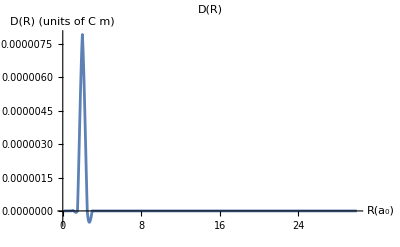

```mathematica
(* Dipole moment in SI units *)
drAUtoSI = 8.478*^-30; (* Cm *)
allDRSI=allDR;
allDRSI[[All,2]] =allDR[[All,2]]*drAUtoSI;
allDRSI

dR =Interpolation[Transpose[{allDR[[All,1]],allDR[[All,2]]}], InterpolationOrder->3];
Plot[dR[r],{r,0.1, maxR}, PlotLabel->"D(R)", AxesLabel->{"R(a_0)", "D(R)(in a.u.)"}, PlotRange->Full]

dRSI =Interpolation[Transpose[{allDRSI[[All,1]],allDRSI[[All,2]]}], InterpolationOrder->3];
Plot[dRSI[r],{r,0.1, maxR}, PlotLabel->"D(R)", AxesLabel->{"R(a_0)", "D(R) (units of C m)"}, PlotRange->Full]
```

```mathematica
aR[R_]:=4/(3hbar cLight^3)(dR[R])^2((vU[R]-vG[R])/hbar)^3;

aRAUtoSI = 4.1341*^16;
aRSI[R_]:=aR[R]*aRAUtoSI;

aRSI2[R_]:=4/(3 hbarSI cLightSI^3)(dRSI[R])^2(((vU[R]-vG[R])4.35974*^-18)/hbarSI)^3;


Plot[aR[r],{r,.1,  10}, PlotLabel->"A(R)", AxesLabel->{"R(a_0)", "A(R)"}, PlotRange->Full]
Plot[aRSI[r],{r,.1,  10}, PlotLabel->"A(R)", AxesLabel->{"R(a_0)", "A(R) (s^-1)"}, PlotRange->Full]
Plot[aRSI2[r],{r,.1,  10}, PlotLabel->"A(R)", AxesLabel->{"R(a_0)", "A(R) (s^-1)"}, PlotRange->Full]
```

-Graphics-

-Graphics-

-Graphics-